```mathematica
data={0,104.,105.6,105.6,115.2,113.6,105.6,108.8,112.,100.8,97.6,97.6,104.,99.2,91.2,94.4,100.8,88.,88.,88.,97.6,97.6,99.2,112.,128.,120.,128.,128.,144.,140.8,139.2,150.4,163.2,163.2,140.8,140.8,147.2,144.,121.6,124.8,129.6,108.8,108.8,107.2,115.2,115.2,100.8,108.8,113.6,97.6,97.6,99.2,110.4,115.2,110.4,128.,142.4,140.8,140.8,142.4,161.6,166.4,153.6,219.2,187.2,180.8,184.,184.,203.2,206.4,214.4,256.,272.,257.6,257.6,262.4,289.6,286.4,268.8,297.6,312.,292.8,292.8,299.2,326.4,316.8,292.8,326.4,334.4,307.2,307.2,291.2,334.4,313.6,281.6,299.2,289.6,251.2,190.4,190.4,200.,179.2,156.8,166.4,160.,140.8,140.8,131.2,145.6,134.4,126.4,134.4,152.,144.,145.6,145.6,171.2,163.2,155.2,163.2,217.6,192.,164.8,164.8,192.,182.4,176.,190.4,225.6,236.8,236.8,240.,268.8,265.6,257.6,281.6,308.8,289.6,289.6,296.,329.6,316.8,302.4,320.,328.,292.8,292.8,288.,297.6,254.4,187.2,179.2,216.,148.8,148.8,150.4,168.,177.6,163.2,182.4,200.,174.4,176.,176.,187.2,166.4,171.2,160.,168.,148.8,148.8,200.,185.6,195.2,185.6,257.6,286.4,286.4,260.8,286.4,329.6,334.4,312.,347.2,369.6,323.2,323.2,344.,372.8,361.6,323.2,345.6,350.4,312.,312.,297.6,299.2,275.2,230.4,193.6,184.,179.2,179.2,140.8,137.6,126.4,115.2,129.6,140.8,139.2,139.2,152.,203.2,172.8,169.6,203.2,259.2,248.,248.,267.2,291.2,284.8,273.6,316.8,321.6,297.6,291.2,291.2,336.,315.2,291.2,328.,320.,286.4,267.2,292.8,292.8,260.8,228.8,203.2,185.6,180.8,153.6,153.6,156.8,139.2,128.,134.4,144.,134.4,137.6,137.6,160.,152.,150.4,203.2,203.2,166.4,169.6,169.6,190.4,198.4,177.6,161.6,156.8,136.,131.2,131.2,140.8,132.8,132.8,150.4,161.6,156.8,196.8,196.8,203.2,193.6,203.2,273.6,289.6,288.,312.,312.,353.6,328.,328.,360.,384.,334.4,352.,352.,384.,344.,342.4,372.8,390.4,337.6,355.2,355.2,384.,336.,331.2,352.,355.2,297.6,300.8,300.8,307.2,283.2,200.,206.4,219.2,166.4,156.8,156.8,155.2,139.2,126.4,139.2,147.2,137.6,156.8,177.6,177.6,177.6,209.6,225.6,222.4,190.4,190.4,196.8,209.6,198.4,190.4,211.2,228.8,217.6,217.6,184.,180.8,160.,145.6,150.4,142.4,131.2,131.2,144.,156.8,152.,148.8,179.2,182.4,176.,176.,219.2,227.2,275.2,272.,339.2,340.8,323.2,323.2,366.4,379.2,352.,336.,388.8,371.2,337.6,340.8,340.8,376.,340.8,321.6,360.,329.6,291.2,281.6,281.6,291.2,211.2,192.,212.8,182.4,158.4,155.2,155.2,158.4,137.6,131.2,142.4,145.6,142.4,156.8,156.8,176.,166.4,169.6,208.,219.2,184.,201.6,201.6,222.4,200.,200.,214.4,203.2,185.6,203.2,203.2,187.2,155.2,145.6,150.4,137.6,131.2,142.4,142.4,158.4,148.8,158.4,180.8,192.,193.6,227.2,227.2,219.2,203.2,212.8,294.4,310.4,288.,323.2,323.2,356.8,320.,339.2,374.4,379.2,339.2,369.6,369.6,371.2,371.2,358.4,392.,388.8,348.8,380.8,380.8,400.,372.8,364.8,396.8,387.2,348.8,348.8,379.2,390.4,358.4,347.2,363.2,339.2,294.4,294.4,300.8,262.4,212.8,203.2,252.8,188.8,163.2,163.2,169.6,163.2,144.,142.4,153.6,148.8,140.8,163.2,163.2,169.6,158.4,153.6,174.4,164.8,150.4,150.4,168.,166.4,150.4,144.,161.6,148.8,137.6,137.6,156.8,156.8,147.2,148.8,176.,168.,160.,168.,168.,180.8,164.8,160.,177.6,160.,145.6,148.8,148.8,152.,139.2,139.2,155.2,155.2,153.6,171.2,171.2,185.6,176.,200.,251.2,222.4,212.8,227.2,227.2,240.,230.4,206.4,201.6,182.4,171.2,176.,176.,180.8,148.8,142.4,148.8,132.8,128.,140.8,140.8,153.6,140.8,153.6,176.,168.,171.2,192.,192.,209.6,208.,251.2,265.6,246.4,275.2,310.4,310.4,336.,302.4,326.4,360.,355.2,328.,328.,361.6,377.6,331.2,353.6,384.,371.2,339.2,339.2,368.,372.8,337.6,334.4,348.8,321.6,288.,288.,294.4,243.2,230.4,249.6,217.6,187.2,171.2,184.,184.,185.6,172.8,185.6,203.2,196.8,185.6,230.4,230.4,232.,212.8,225.6,217.6,196.8,179.2,196.8,196.8,187.2,164.8,171.2,176.,164.8,160.,192.,192.,198.4,235.2,227.2,244.8,283.2,281.6,344.,344.,342.4,323.2,332.8,382.4,356.8,342.4,342.4,380.8,380.8,350.4,356.8,398.4,363.2,348.8,374.4,374.4,380.8,350.4,358.4,392.,356.8,344.,368.,368.,364.8,332.8,339.2,358.4,318.4,302.4,310.4,310.4,289.6,217.6,238.4,248.,188.8,180.8,190.4,190.4,177.6,160.,166.4,172.8,152.,150.4,164.8,164.8,172.8,153.6,168.,187.2,169.6,177.6,198.4,209.6,209.6,204.8,252.8,257.6,209.6,217.6,240.,240.,246.4,216.,230.4,243.2,225.6,232.,236.8,236.8,212.8,182.4,192.,198.4,182.4,168.,168.,180.8,174.4,153.6,166.4,177.6,171.2,174.4,174.4,196.8,196.8,185.6,204.8,219.2,225.6,244.8,244.8,265.6,257.6,251.2,299.2,315.2,299.2,305.6,305.6,337.6,332.8,308.8,345.6,356.8,331.2,316.8,316.8,352.,352.,323.2,361.6,364.8,332.8,318.4,361.6,361.6,339.2,307.2,337.6,331.2,292.8,275.2,288.,288.,257.6,228.8,219.2,208.,182.4,171.2,171.2,187.2,171.2,156.8,166.4,184.,172.8,177.6,177.6,208.,198.4,190.4,204.8,225.6,222.4,224.,256.,256.,248.,236.8,249.6,254.4,227.2,227.2,224.,224.,206.4,195.2,203.2,206.4,184.,182.4,196.8,196.8,180.8,176.,188.8,203.2,179.2,188.8,209.6,209.6,192.,190.4,208.,224.,217.6,240.,264.,264.,272.,251.2,296.,316.8,281.6,302.4,332.8,332.8,332.8,307.2,337.6,355.2,310.4,331.2,360.,360.,352.,321.6,348.8,358.4,329.6,328.,347.2,347.2,328.,296.,316.8,315.2,264.,262.4,262.4,262.4,224.,204.8,217.6,214.4,193.6,198.4,206.4,206.4,193.6,179.2,204.8,211.2,195.2,209.6,224.,224.,214.4,203.2,254.4,252.8,244.8,265.6,278.4,278.4,259.2,241.6,278.4,264.,230.4,219.2,232.,232.,211.2,196.8,222.4,212.8,188.8,187.2,206.4,206.4,188.8,179.2,208.,200.,187.2,192.,219.2,219.2,201.6,198.4,214.4,222.4,227.2,225.6,225.6,275.2,257.6,256.,300.8,304.,286.4,302.4,302.4,332.8,310.4,308.8,339.2,336.,318.4,337.6,371.2,371.2,334.4,334.4,364.8,352.,331.2,348.8,374.4,374.4,324.8,320.,336.,307.2,284.8,273.6,262.4,262.4,220.8,217.6,238.4,240.,209.6,225.6,241.6,241.6,211.2,222.4,246.4,244.8,219.2,235.2,251.2,251.2,219.2,227.2,252.8,246.4,214.4,230.4,241.6,241.6,227.2,219.2,241.6,240.,219.2,240.,240.,252.8,236.8,232.,251.2,243.2,222.4,240.,240.,249.6,236.8,236.8,268.8,264.,268.8,318.4,334.4,334.4,312.,326.4,356.8,347.2,323.2,364.8,364.8,372.8,342.4,329.6,379.2,358.4,326.4,361.6,353.6,353.6,315.2,292.8,324.8,270.4,240.,248.,248.,243.2,217.6,211.2,241.6,227.2,211.2,220.8,220.8,236.8,217.6,217.6,252.8,236.8,222.4,235.2,235.2,264.,249.6,243.2,307.2,294.4,286.4,308.8,308.8,324.8,302.4,312.,345.6,329.6,320.,345.6,345.6,358.4,332.8,342.4,374.4,345.6,334.4,358.4,358.4,356.8,326.4,331.2,352.,304.,288.,278.4,257.6,257.6,214.4,216.,233.6,203.2,198.4,214.4,227.2,227.2,201.6,211.2,228.8,203.2,201.6,219.2,227.2,227.2,198.4,211.2,232.,224.,206.4,225.6,233.6,233.6,200.,214.4,233.6,230.4,224.,257.6,265.6,265.6,232.,244.8,254.4,240.,227.2,244.8,248.,248.,227.2,241.6,260.8,257.6,257.6,294.4,334.4,334.4,331.2,356.8,377.6,350.4,324.8,368.,360.,360.,326.4,350.4,360.,329.6,310.4,360.,350.4,350.4,320.,350.4,358.4,328.,308.8,355.2,339.2,339.2,310.4,313.6,348.8,320.,305.6,353.6,337.6,337.6,310.4,318.4,353.6,323.2,312.,363.2,345.6,345.6,324.8,337.6,369.6,337.6,329.6,355.2,355.2,347.2,300.8,276.8,281.6,246.4,230.4,244.8,244.8,238.4,230.4,267.2,323.2,304.,320.,358.4,358.4,352.,340.8,366.4,401.6,356.8,363.2,396.8,396.8,374.4,360.,385.6,416.,364.8,372.8,406.4,406.4,374.4,361.6,388.8,414.4,360.,371.2,404.8,406.4,406.4,358.4,385.6,408.,353.6,368.,401.6,396.8,396.8,355.2,385.6,404.8,350.4,368.,400.,390.4,390.4,353.6,384.,398.4,366.4,363.2,388.8,388.8,374.4,342.4,368.,374.4,339.2,334.4,347.2,316.8,316.8,276.8,283.2,265.6,219.2,171.2,160.,120.,120.,44.8,30.4,30.4,27.2,30.4,32.,32.,32.,30.4,35.2,35.2,32.,35.2,36.8,33.6,33.6,32.,36.8,35.2,32.,32.,35.2,33.6,33.6,30.4,36.8,35.2,32.,32.,36.8,36.8,33.6,32.,33.6,35.2,32.,32.,36.8,33.6,33.6,32.,33.6,35.2,32.,33.6,36.8,36.8,33.6,32.,35.2,35.2,32.,33.6,36.8,33.6,33.6,32.,35.2,35.2,32.,33.6,36.8,36.8,33.6,33.6,35.2,35.2,32.,33.6,36.8,36.8,32.,32.,35.2,36.8,32.,33.6,36.8,36.8,32.,33.6,36.8,36.8,32.,35.2,36.8,36.8,32.,33.6,36.8,36.8,32.,35.2,38.4,35.2,35.2,33.6,36.8,36.8,33.6,35.2,38.4,35.2,35.2,33.6,36.8,36.8,33.6,36.8,38.4,35.2,35.2,35.2,38.4,36.8,33.6,36.8,36.8,33.6,33.6,33.6,36.8,35.2,32.,35.2,36.8,33.6,33.6,35.2,36.8,35.2,32.,36.8,36.8,33.6,33.6,32.,38.4,35.2,32.,36.8,36.8,33.6,33.6,32.,38.4,35.2,32.,36.8,36.8,33.6,33.6,32.,36.8,33.6,32.,32.,33.6,33.6,30.4,30.4,35.2,33.6,30.4,33.6,35.2,32.,32.,32.,35.2,32.,30.4,32.,33.6,30.4,30.4,30.4,33.6,32.,30.4,33.6,33.6,33.6,32.,32.,35.2,32.,30.4,33.6,35.2,30.4,30.4,32.,35.2,32.,32.,33.6,35.2,35.2,32.,33.6,36.8,32.,32.,35.2,36.8,36.8,32.,33.6,36.8,35.2,32.,35.2,36.8,36.8,32.,33.6,36.8,35.2,32.,33.6,35.2,30.4,30.4,32.,35.2,33.6,32.,35.2,35.2,32.,32.,33.6,35.2,32.,30.4,32.,32.,28.8,28.8,30.4,28.8,30.4,28.8,33.6,33.6,30.4,30.4,33.6,35.2,33.6,32.,36.8,35.2,32.,36.8,36.8,36.8,33.6,32.,36.8,35.2,33.6,33.6,36.8,36.8,33.6,32.,36.8,35.2,32.,32.,32.,36.8,33.6,32.,36.8,35.2,32.,32.,33.6,36.8,33.6,32.,36.8,35.2,32.,33.6,33.6,36.8,33.6,32.,35.2,35.2,32.,32.,35.2,36.8,33.6,33.6,36.8,35.2,33.6,33.6,35.2,36.8,33.6,33.6,36.8,35.2,35.2,35.2,35.2,38.4,33.6,33.6,36.8,33.6,33.6,32.,35.2,36.8,32.,33.6,36.8,36.8,36.8,32.,35.2,38.4,32.,33.6,36.8,36.8,36.8,33.6,36.8,38.4,32.,33.6,38.4,36.8,36.8,33.6,36.8,38.4,35.2,35.2,38.4,36.8,36.8,33.6,36.8,38.4,35.2,35.2,80.,184.,289.6,289.6,350.4,366.4,345.6,366.4,393.6,374.4,344.,344.,388.8,390.4,356.8,377.6,398.4,372.8,345.6,345.6,393.6,388.8,353.6,379.2,396.8,369.6,344.,344.,395.2,385.6,352.,348.8,396.8,366.4,344.,344.,396.8,382.4,348.8,350.4,395.2,361.6,344.,344.,396.8,377.6,345.6,350.4,388.8,356.8,356.8,342.4,368.,372.8,344.,353.6,388.8,353.6,353.6,371.2,371.2,369.6,344.,356.8,385.6,353.6,355.2,355.2,388.8,384.,361.6,379.2,412.8,369.6,366.4,366.4,396.8,380.8,360.,379.2,409.6,361.6,361.6,361.6,392.,369.6,352.,374.4,403.2,352.,356.8,356.8,388.8,396.8,345.6,368.,395.2,342.4,342.4,350.4,382.4,387.2,340.8,368.,393.6,372.8,372.8,356.8,390.4,390.4,350.4,382.4,404.8,380.8,380.8,368.,401.6,395.2,355.2,387.2,404.8,376.,371.2,371.2,403.2,392.,358.4,388.8,403.2,371.2,371.2,372.8,403.2,388.8,353.6,392.,400.,368.,376.,376.,403.2,384.,353.6,395.2,398.4,364.8,350.4,350.4,406.4,382.4,352.,400.,398.4,363.2,353.6,353.6,406.4,379.2,352.,403.2,396.8,361.6,355.2,355.2,406.4,376.,350.4,366.4,390.4,356.8,355.2,355.2,403.2,372.8,350.4,371.2,388.8,356.8,358.4,358.4,401.6,368.,352.,374.4,385.6,355.2,360.,360.,393.6,366.4,352.,377.6,382.4,353.6,363.2,363.2,396.8,363.2,353.6,380.8,379.2,352.,352.,366.4,400.,360.,355.2,384.,408.,353.6,353.6,369.6,403.2,358.4,356.8,388.8,408.,353.6,353.6,372.8,406.4,358.4,360.,392.,406.4,352.,352.,374.4,403.2,390.4,360.,393.6,403.2,353.6,353.6,379.2,406.4,387.2,363.2,398.4,401.6,353.6,353.6,382.4,406.4,384.,366.4,400.,398.4,364.8,384.,384.,406.4,380.8,369.6,401.6,396.8,361.6,361.6,387.2,404.8,376.,352.,403.2,393.6,358.4,358.4,390.4,403.2,372.8,352.,404.8,390.4,356.8,356.8,395.2,403.2,369.6,352.,406.4,387.2,355.2,360.,360.,400.,366.4,350.4,403.2,380.8,352.,361.6,361.6,396.8,363.2,352.,406.4,379.2,352.,364.8,364.8,395.2,360.,353.6,382.4,376.,350.4,368.,368.,392.,356.8,355.2,385.6,371.2,350.4,369.6,369.6,387.2,353.6,355.2,387.2,366.4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
```

```mathematica
Sort[data]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,27.2,28.8,28.8,28.8,28.8,30.4,30.4,30.4,30.4,30.4,30.4,30.4,30.4,30.4,30.4,30.4,30.4,30.4,30.4,30.4,30.4,30.4,30.4,30.4,30.4,30.4,30.4,30.4,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,32.,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,33.6,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,35.2,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,36.8,38.4,38.4,38.4,38.4,38.4,38.4,38.4,38.4,38.4,38.4,38.4,38.4,38.4,44.8,80.,88.,88.,88.,91.2,94.4,97.6,97.6,97.6,97.6,97.6,97.6,99.2,99.2,99.2,100.8,100.8,100.8,104.,104.,105.6,105.6,105.6,107.2,108.8,108.8,108.8,108.8,110.4,110.4,112.,112.,113.6,113.6,115.2,115.2,115.2,115.2,115.2,120.,120.,120.,121.6,124.8,126.4,126.4,126.4,128.,128.,128.,128.,128.,128.,129.6,129.6,131.2,131.2,131.2,131.2,131.2,131.2,131.2,132.8,132.8,132.8,134.4,134.4,134.4,134.4,136.,137.6,137.6,137.6,137.6,137.6,137.6,137.6,137.6,139.2,139.2,139.2,139.2,139.2,139.2,139.2,139.2,140.8,140.8,140.8,140.8,140.8,140.8,140.8,140.8,140.8,140.8,140.8,140.8,140.8,140.8,142.4,142.4,142.4,142.4,142.4,142.4,142.4,142.4,142.4,144.,144.,144.,144.,144.,144.,144.,145.6,145.6,145.6,145.6,145.6,145.6,145.6,147.2,147.2,147.2,148.8,148.8,148.8,148.8,148.8,148.8,148.8,148.8,148.8,148.8,148.8,148.8,148.8,150.4,150.4,150.4,150.4,150.4,150.4,150.4,150.4,150.4,150.4,152.,152.,152.,152.,152.,152.,153.6,153.6,153.6,153.6,153.6,153.6,153.6,153.6,153.6,153.6,155.2,155.2,155.2,155.2,155.2,155.2,155.2,156.8,156.8,156.8,156.8,156.8,156.8,156.8,156.8,156.8,156.8,156.8,156.8,156.8,158.4,158.4,158.4,158.4,158.4,160.,160.,160.,160.,160.,160.,160.,160.,160.,160.,161.6,161.6,161.6,161.6,163.2,163.2,163.2,163.2,163.2,163.2,163.2,163.2,163.2,163.2,164.8,164.8,164.8,164.8,164.8,164.8,164.8,164.8,166.4,166.4,166.4,166.4,166.4,166.4,166.4,166.4,166.4,166.4,168.,168.,168.,168.,168.,168.,168.,168.,168.,168.,169.6,169.6,169.6,169.6,169.6,169.6,169.6,171.2,171.2,171.2,171.2,171.2,171.2,171.2,171.2,171.2,171.2,171.2,171.2,171.2,172.8,172.8,172.8,172.8,172.8,174.4,174.4,174.4,174.4,174.4,176.,176.,176.,176.,176.,176.,176.,176.,176.,176.,176.,176.,176.,177.6,177.6,177.6,177.6,177.6,177.6,177.6,177.6,177.6,177.6,177.6,179.2,179.2,179.2,179.2,179.2,179.2,179.2,179.2,179.2,180.8,180.8,180.8,180.8,180.8,180.8,180.8,180.8,180.8,182.4,182.4,182.4,182.4,182.4,182.4,182.4,182.4,182.4,184.,184.,184.,184.,184.,184.,184.,184.,184.,184.,185.6,185.6,185.6,185.6,185.6,185.6,185.6,185.6,185.6,187.2,187.2,187.2,187.2,187.2,187.2,187.2,187.2,187.2,187.2,188.8,188.8,188.8,188.8,188.8,188.8,190.4,190.4,190.4,190.4,190.4,190.4,190.4,190.4,190.4,190.4,190.4,192.,192.,192.,192.,192.,192.,192.,192.,192.,192.,192.,193.6,193.6,193.6,193.6,193.6,195.2,195.2,195.2,196.8,196.8,196.8,196.8,196.8,196.8,196.8,196.8,196.8,196.8,196.8,196.8,198.4,198.4,198.4,198.4,198.4,198.4,198.4,198.4,198.4,198.4,200.,200.,200.,200.,200.,200.,200.,200.,200.,201.6,201.6,201.6,201.6,201.6,201.6,203.2,203.2,203.2,203.2,203.2,203.2,203.2,203.2,203.2,203.2,203.2,203.2,203.2,203.2,203.2,203.2,203.2,203.2,203.2,204.8,204.8,204.8,204.8,204.8,206.4,206.4,206.4,206.4,206.4,206.4,206.4,206.4,206.4,206.4,208.,208.,208.,208.,208.,208.,209.6,209.6,209.6,209.6,209.6,209.6,209.6,209.6,209.6,209.6,211.2,211.2,211.2,211.2,211.2,211.2,211.2,211.2,211.2,212.8,212.8,212.8,212.8,212.8,212.8,212.8,214.4,214.4,214.4,214.4,214.4,214.4,214.4,214.4,214.4,216.,216.,216.,217.6,217.6,217.6,217.6,217.6,217.6,217.6,217.6,217.6,217.6,217.6,217.6,217.6,219.2,219.2,219.2,219.2,219.2,219.2,219.2,219.2,219.2,219.2,219.2,219.2,219.2,219.2,219.2,219.2,220.8,220.8,220.8,222.4,222.4,222.4,222.4,222.4,222.4,222.4,222.4,222.4,224.,224.,224.,224.,224.,224.,224.,224.,224.,225.6,225.6,225.6,225.6,225.6,225.6,225.6,225.6,225.6,225.6,227.2,227.2,227.2,227.2,227.2,227.2,227.2,227.2,227.2,227.2,227.2,227.2,227.2,227.2,227.2,227.2,227.2,227.2,228.8,228.8,228.8,228.8,230.4,230.4,230.4,230.4,230.4,230.4,230.4,230.4,230.4,230.4,230.4,232.,232.,232.,232.,232.,232.,232.,233.6,233.6,233.6,233.6,235.2,235.2,235.2,235.2,236.8,236.8,236.8,236.8,236.8,236.8,236.8,236.8,236.8,236.8,238.4,238.4,238.4,240.,240.,240.,240.,240.,240.,240.,240.,240.,240.,240.,240.,240.,241.6,241.6,241.6,241.6,241.6,241.6,241.6,241.6,243.2,243.2,243.2,243.2,243.2,244.8,244.8,244.8,244.8,244.8,244.8,244.8,244.8,244.8,246.4,246.4,246.4,246.4,246.4,248.,248.,248.,248.,248.,248.,248.,248.,249.6,249.6,249.6,249.6,251.2,251.2,251.2,251.2,251.2,251.2,251.2,251.2,252.8,252.8,252.8,252.8,252.8,252.8,254.4,254.4,254.4,254.4,256.,256.,256.,256.,257.6,257.6,257.6,257.6,257.6,257.6,257.6,257.6,257.6,257.6,257.6,257.6,257.6,259.2,259.2,260.8,260.8,260.8,262.4,262.4,262.4,262.4,262.4,262.4,262.4,264.,264.,264.,264.,264.,264.,265.6,265.6,265.6,265.6,265.6,265.6,265.6,267.2,267.2,267.2,268.8,268.8,268.8,268.8,270.4,272.,272.,272.,273.6,273.6,273.6,275.2,275.2,275.2,275.2,275.2,276.8,276.8,278.4,278.4,278.4,278.4,281.6,281.6,281.6,281.6,281.6,281.6,281.6,283.2,283.2,283.2,284.8,284.8,286.4,286.4,286.4,286.4,286.4,286.4,286.4,288.,288.,288.,288.,288.,288.,288.,288.,289.6,289.6,289.6,289.6,289.6,289.6,289.6,289.6,291.2,291.2,291.2,291.2,291.2,291.2,291.2,292.8,292.8,292.8,292.8,292.8,292.8,292.8,292.8,292.8,294.4,294.4,294.4,294.4,294.4,294.4,296.,296.,296.,297.6,297.6,297.6,297.6,297.6,299.2,299.2,299.2,299.2,299.2,300.8,300.8,300.8,300.8,300.8,302.4,302.4,302.4,302.4,302.4,302.4,302.4,304.,304.,304.,305.6,305.6,305.6,307.2,307.2,307.2,307.2,307.2,307.2,307.2,308.8,308.8,308.8,308.8,308.8,308.8,310.4,310.4,310.4,310.4,310.4,310.4,310.4,310.4,310.4,310.4,312.,312.,312.,312.,312.,312.,312.,312.,312.,313.6,313.6,315.2,315.2,315.2,315.2,316.8,316.8,316.8,316.8,316.8,316.8,316.8,316.8,316.8,318.4,318.4,318.4,318.4,318.4,320.,320.,320.,320.,320.,320.,320.,320.,321.6,321.6,321.6,321.6,323.2,323.2,323.2,323.2,323.2,323.2,323.2,323.2,323.2,323.2,323.2,323.2,324.8,324.8,324.8,324.8,324.8,326.4,326.4,326.4,326.4,326.4,326.4,326.4,328.,328.,328.,328.,328.,328.,328.,328.,328.,329.6,329.6,329.6,329.6,329.6,329.6,329.6,329.6,331.2,331.2,331.2,331.2,331.2,331.2,331.2,331.2,332.8,332.8,332.8,332.8,332.8,332.8,332.8,332.8,332.8,334.4,334.4,334.4,334.4,334.4,334.4,334.4,334.4,334.4,334.4,334.4,334.4,334.4,336.,336.,336.,336.,336.,336.,337.6,337.6,337.6,337.6,337.6,337.6,337.6,337.6,337.6,337.6,337.6,339.2,339.2,339.2,339.2,339.2,339.2,339.2,339.2,339.2,339.2,339.2,339.2,340.8,340.8,340.8,340.8,340.8,340.8,342.4,342.4,342.4,342.4,342.4,342.4,342.4,342.4,342.4,342.4,344.,344.,344.,344.,344.,344.,344.,344.,344.,344.,344.,344.,344.,344.,344.,345.6,345.6,345.6,345.6,345.6,345.6,345.6,345.6,345.6,345.6,345.6,345.6,345.6,347.2,347.2,347.2,347.2,347.2,347.2,347.2,348.8,348.8,348.8,348.8,348.8,348.8,348.8,348.8,348.8,348.8,350.4,350.4,350.4,350.4,350.4,350.4,350.4,350.4,350.4,350.4,350.4,350.4,350.4,350.4,350.4,350.4,350.4,350.4,350.4,350.4,350.4,352.,352.,352.,352.,352.,352.,352.,352.,352.,352.,352.,352.,352.,352.,352.,352.,352.,352.,352.,352.,352.,352.,352.,352.,352.,352.,352.,353.6,353.6,353.6,353.6,353.6,353.6,353.6,353.6,353.6,353.6,353.6,353.6,353.6,353.6,353.6,353.6,353.6,353.6,353.6,353.6,353.6,353.6,353.6,353.6,353.6,353.6,353.6,353.6,353.6,355.2,355.2,355.2,355.2,355.2,355.2,355.2,355.2,355.2,355.2,355.2,355.2,355.2,355.2,355.2,355.2,355.2,355.2,355.2,355.2,355.2,356.8,356.8,356.8,356.8,356.8,356.8,356.8,356.8,356.8,356.8,356.8,356.8,356.8,356.8,356.8,356.8,356.8,356.8,356.8,356.8,356.8,356.8,358.4,358.4,358.4,358.4,358.4,358.4,358.4,358.4,358.4,358.4,358.4,358.4,358.4,358.4,358.4,358.4,358.4,358.4,358.4,358.4,360.,360.,360.,360.,360.,360.,360.,360.,360.,360.,360.,360.,360.,360.,360.,360.,360.,360.,360.,360.,361.6,361.6,361.6,361.6,361.6,361.6,361.6,361.6,361.6,361.6,361.6,361.6,361.6,361.6,361.6,361.6,361.6,363.2,363.2,363.2,363.2,363.2,363.2,363.2,363.2,363.2,363.2,363.2,364.8,364.8,364.8,364.8,364.8,364.8,364.8,364.8,364.8,364.8,364.8,366.4,366.4,366.4,366.4,366.4,366.4,366.4,366.4,366.4,366.4,366.4,366.4,366.4,366.4,368.,368.,368.,368.,368.,368.,368.,368.,368.,368.,368.,368.,368.,368.,368.,369.6,369.6,369.6,369.6,369.6,369.6,369.6,369.6,369.6,369.6,369.6,369.6,369.6,371.2,371.2,371.2,371.2,371.2,371.2,371.2,371.2,371.2,371.2,371.2,371.2,371.2,371.2,371.2,372.8,372.8,372.8,372.8,372.8,372.8,372.8,372.8,372.8,372.8,372.8,372.8,372.8,372.8,374.4,374.4,374.4,374.4,374.4,374.4,374.4,374.4,374.4,374.4,374.4,374.4,374.4,374.4,376.,376.,376.,376.,376.,376.,376.,377.6,377.6,377.6,377.6,377.6,379.2,379.2,379.2,379.2,379.2,379.2,379.2,379.2,379.2,379.2,379.2,380.8,380.8,380.8,380.8,380.8,380.8,380.8,380.8,380.8,380.8,380.8,382.4,382.4,382.4,382.4,382.4,382.4,382.4,382.4,384.,384.,384.,384.,384.,384.,384.,384.,384.,384.,384.,385.6,385.6,385.6,385.6,385.6,385.6,385.6,387.2,387.2,387.2,387.2,387.2,387.2,387.2,387.2,388.8,388.8,388.8,388.8,388.8,388.8,388.8,388.8,388.8,388.8,388.8,388.8,388.8,388.8,388.8,390.4,390.4,390.4,390.4,390.4,390.4,390.4,390.4,390.4,390.4,390.4,392.,392.,392.,392.,392.,392.,392.,393.6,393.6,393.6,393.6,393.6,393.6,395.2,395.2,395.2,395.2,395.2,395.2,395.2,396.8,396.8,396.8,396.8,396.8,396.8,396.8,396.8,396.8,396.8,396.8,396.8,396.8,396.8,396.8,398.4,398.4,398.4,398.4,398.4,398.4,398.4,400.,400.,400.,400.,400.,400.,400.,401.6,401.6,401.6,401.6,401.6,401.6,403.2,403.2,403.2,403.2,403.2,403.2,403.2,403.2,403.2,403.2,403.2,403.2,403.2,403.2,404.8,404.8,404.8,404.8,404.8,404.8,406.4,406.4,406.4,406.4,406.4,406.4,406.4,406.4,406.4,406.4,406.4,406.4,406.4,406.4,408.,408.,408.,409.6,412.8,414.4,416.}

```mathematica
(*This datat is the result of a school competiton. The competiton is the person to get the closest to a number(Possibly down to a Tenth) between 0 and 450 inclusive.*)
```

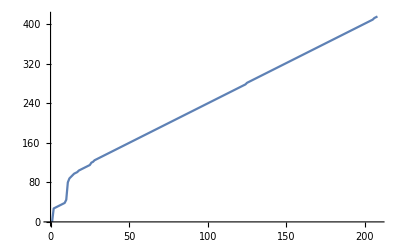

```mathematica
(*This data is to show close to linear growth of guesses so this excluding duplicates*)
ListLinePlot[DeleteDuplicates[Sort[data]]]
```

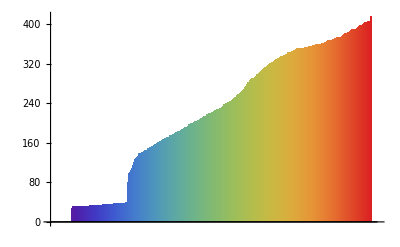

```mathematica
(*This is shows all of the guesses in a barchart format, from 0 up.*)
BarChart[Sort[data],ChartStyle->"Rainbow", BarSpacing->Large]
```

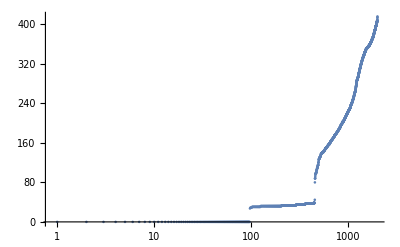

```mathematica
(*This is a show of all of the guesses from 0 up, the graph really shows the ranges people guessed in, and who all guessed the same number. For example you can see a lot more people were in the 0 - 10 range than any other.*)
ListLogLinearPlot[Sort[data]]
```

```mathematica
Length[data]
```

2000